## MATHEMATICA RESEARCH PROJECT:- “GENDER RECOGNITION BY VOICE”

#### By, Nisarga.G 19203753

## Introduction

## Insights from voice data set:

Have you ever wondered how Siri ,Ok google, Alexa differentiate voices and responds only if its you???

Work processes become more efficient because document processing times become shorter. 
Documents can be generated up to three times as fast with speech recognition as they can if they are typed.
Voice recognition is an alternative to typing on a keyboard. Put simply, you talk to the computer and your words appear on the screen. The software has been developed to provide a fast method of writing on a computer and can help people with a variety of disabilities.Also ,it is very important to differentiate people by voices for security  and authentication purposes.

This voice dataset has many entries of various parameters of  human voice and a label male or female. Based on parameters,I am going to simply classify whether it is male or female , which I believe is the primary step for speech analysis . The aim of this project is to perform various classification methods on the voice dataset and find out which classification method is the best for this dataset. I would prefer performing analysis on dataset and preparing the data  well before moving to classification.

## Importing voice dataset:

```mathematica
voiceData=Import["Desktop/voice.csv"];
```

The voice dataset looks like:

```mathematica
voiceData//Dataset
```

Dataset[<>]

After importing the dataset ,it is very important to make the association with the header names and only data for the further data manipulation.

```mathematica
header=voiceData[[1]];
datatest=voiceData[[2;;]];
voicedata=Thread[header->#]&/@datatest//Map[Association]
```

{<|meanfreq→0.059781,sd→0.0642413,median→0.0320269,Q25→0.0150715,Q75→0.0901934,IQR→0.075122,skew→12.8635,kurt→274.403,sp.ent→0.893369,sfm→0.491918,mode→0,centroid→0.059781,meanfun→0.0842791,minfun→0.0157017,maxfun→0.275862,meandom→0.0078125,mindom→0.0078125,maxdom→0.0078125,dfrange→0,modindx→0,label→male|>,<|1|>,3164,<|1|>,<|1|>}
 |  |  |  |

For few plotting the dataset should be a list or Dataset format.

```mathematica
Voicedata=Thread[header->#]&/@datatest//Map[Association]//Dataset;
```

For applying statistical calculation on the dataset , we should convert the categorical variable of string type to numeric as calculations can be applied to only numeric data.

```mathematica
voicedata1=voicedata/.{"male"-> 1,"female"-> 0};
```

Look at the variables name of data:

```mathematica
voiceData[[1]]
```

{meanfreq,sd,median,Q25,Q75,IQR,skew,kurt,sp.ent,sfm,mode,centroid,meanfun,minfun,maxfun,meandom,mindom,maxdom,dfrange,modindx,label}

## A Short description of each feature:

meanfreq:mean frequency (in kHz)
sd:standard deviation of frequency
median:median frequency (in kHz)
Q25:first quantile (in kHz)
Q75:third quantile (in kHz)
IQR:interquantile range (in kHz)
skew:skewness 
kurt:kurtosis 
sp.ent:spectral entropy
sfm:spectral flatness
mode:mode frequency
centroid:frequency centroid 
peakf:peak frequency (frequency with highest energy)
meanfun:average of fundamental frequency measured across acoustic signal
minfun:minimum fundamental frequency measured across acoustic signal
maxfun:maximum fundamental frequency measured across acoustic signal
meandom:average of dominant frequency measured across acoustic signal
mindom:minimum of dominant frequency measured across acoustic signal
maxdom:maximum of dominant frequency measured across acoustic signal
dfrange:range of dominant frequency measured across acoustic signal
modindx:modulation index.Calculated as the accumulated absolute difference between adjacent measurements of fundamental frequencies divided by the frequency range

label:male or female

Note that we have 3168 voice samples and for each of sample 20 different acoustic properties are recorded.Finally the'label' column is the target variable which we have to predict which is the gender of the person

## Summary of voice dataset:

```mathematica
Mean[voicedata1];
```

```mathematica
Max[voicedata1[[All,1]]];
```

```mathematica
Median[voicedata1];
```

```mathematica
Variance[voicedata1];
```

```mathematica
StandardDeviation[voicedata1];
```

```mathematica
Quantile[voicedata1,1/4];
```

```mathematica
Quantile[voicedata1,3/4];
```

```mathematica
summary={{"Column Name","Mean","Median","Max","variance","standard deviation","1st Quartile","2nd Quartile"},{"meanfreq",0.180907,0.184838,0.251124,0.000895077,0.0299178,0.163643,0.199138},{"sd",0.057126,0.0591551,0.115273,0.000277297,0.0166522,0.0419357,0.0670193},{"median",0.185621,0.190032,0.261224,0.00132206,0.036,0.1695,0.2106},{"Q25",0.140,0.140,0.247,0.0023,0.048,0.111,0.1759},{"Q75",0.224,0.2256,0.273,0.00055,0.0236,0.208,0.243},{"IQR",0.084,0.094,0.2522,0.0018,0.042,0.042,0.1141},{"skew",3.14,2.19,34.72,17.98,4.24,1.64,2.93},{"kurt",36.56,8.31,1309.6,18205.7,134.92,5.66,13.64},{"sp.ent",0.0895,0.90,0.98,0.002,0.044,0.86,0.928},{"sfm",0.408,0.396,0.8429,0.03,0.177,0.257,0.533},{"mode",0.165,0.186,0.28,0.005,0.077,0.118,0.221},{"centroid",0.18,0.184,0.251,0.009,0.0299,0.163,0.199},{"meanfun",0.142,0.140,0.237,0.0010,0.032,0.116,0.169},{"minfun",0.036,0.046,0.204,0.00036,0.0192,0.018,0.047},{"maxfun",0.258,0.2711,0.279,0.00090,0.0300,0.253,0.277},{"meandom",0.829,0.765,2.957,0.275,0.525,0.419,1.177},{"mindom",0.052,0.02,0.4589,0.004,0.06,0.007,0.07},{"maxdom",5.047,4.99,21.86,12.39,3.52,2.07,7},{"dfrange",4.99,4.94,21.84,12.39,3.52,2.039,6.99},{"modindx",0.173,0.139,0.93,0.014,0.11,0.99,0.20}}//Dataset
```

Dataset[<>]

## Checking Missing Values:

```mathematica
Count[voicedata1,_Missing]
```

0

There are no missing values in the dataset.

## Univariate Analysis:

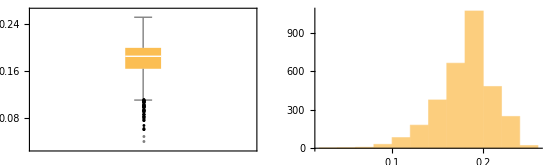

```mathematica
GraphicsGrid[{{BoxWhiskerChart[voicedata[[All,1]],"Outliers"],Histogram[voicedata[[All,1]]]}}]
```

INFERENCES FROM THE PLOT--
1) First of all note that the values are in compliance with that observed from describe method data frame..

2) Note that we have a couple of outliers w.r.t. to 1.5 quartile rule (represented by a ‘dot’ in the box plot).Removing these data points or outliers leaves us with around 3104 values.

3) Also note from the hist plot that the distribution seems to be a bit -ve skewed hence we can normalize to make the distribution a bit more symmetric.

4) LASTLY NOTE THAT A LEFT TAIL DISTRIBUTION HAS MORE OUTLIERS ON THE SIDE BELOW TO Q1 AS EXPECTED AND A RIGHT TAIL HAS ABOVE THE Q3.

Similarly other plots can be inferenced.

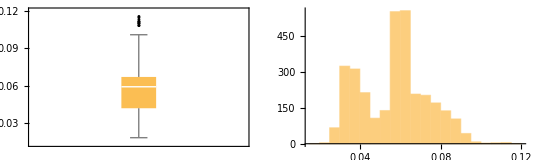

```mathematica
GraphicsGrid[{{BoxWhiskerChart[voicedata[[All,2]],"Outliers"],Histogram[voicedata[[All,2]]]}}]
```

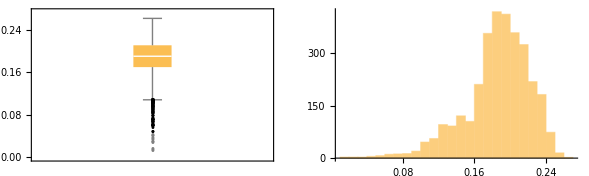

```mathematica
GraphicsGrid[{{BoxWhiskerChart[voicedata[[All,3]],"Outliers"],Histogram[voicedata[[All,3]]]}}]
```

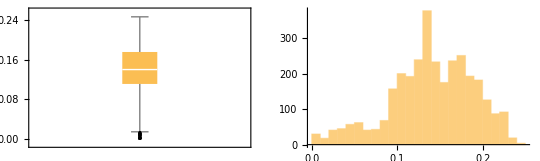

```mathematica
GraphicsGrid[{{BoxWhiskerChart[voicedata[[All,4]],"Outliers"],Histogram[voicedata[[All,4]]]}}]
```

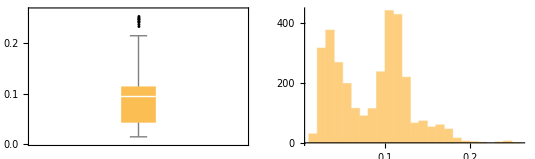

```mathematica
GraphicsGrid[{{BoxWhiskerChart[voicedata[[All,6]],"Outliers"],Histogram[voicedata[[All,6]]]}}]
```

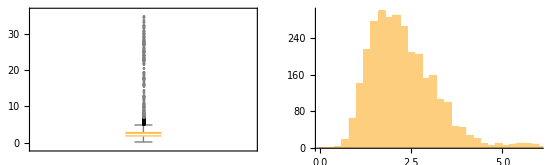

```mathematica
GraphicsGrid[{{BoxWhiskerChart[voicedata[[All,7]],"Outliers"],Histogram[voicedata[[All,7]]]}}]
```

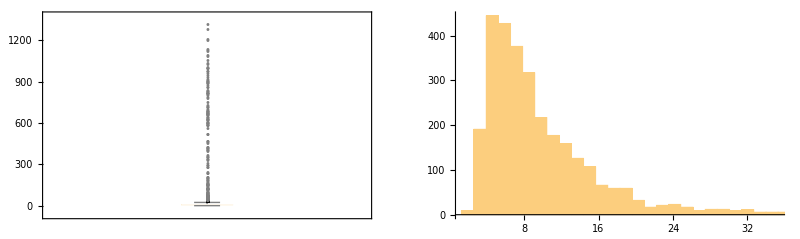

```mathematica
GraphicsGrid[{{BoxWhiskerChart[voicedata[[All,8]],"Outliers"],Histogram[voicedata[[All,8]]]}}]
```

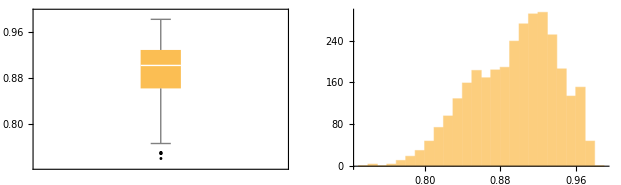

```mathematica
GraphicsGrid[{{BoxWhiskerChart[voicedata[[All,9]],"Outliers"],Histogram[voicedata[[All,9]]]}}]
```

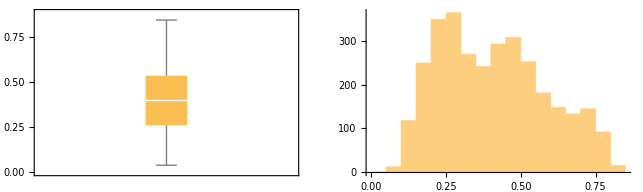

```mathematica
GraphicsGrid[{{BoxWhiskerChart[voicedata[[All,10]],"Outliers"],Histogram[voicedata[[All,10]]]}}]
```

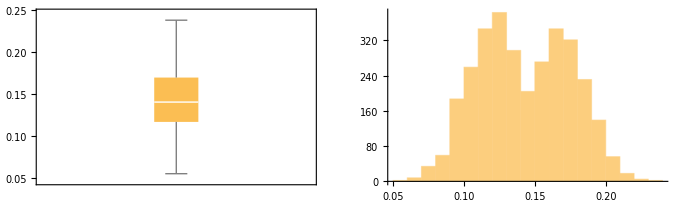

```mathematica
GraphicsGrid[{{BoxWhiskerChart[voicedata[[All,13]],"Outliers"],Histogram[voicedata[[All,13]]]}}]
```

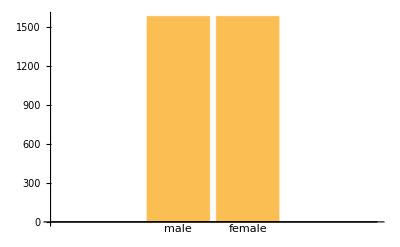

```mathematica
BarChart[Counts[Voicedata[All,"label"]],ChartLabels->Automatic]
```

```mathematica
c=Counts[Voicedata[All,"label"]]
```

Dataset[<>]

Note that there are equal no of observations for the ‘males’ and the ‘females’. Hence it is a balanced class problem.

## Bivariate Analysis: Correlation b/w Features:

In this section I have analyzed the correlation between different features. To do it I have plotted a ‘heat map’ which clearly visualizes the co relation between different features.

```mathematica
m={voicedata[[All,1]],voicedata[[All,2]],voicedata[[All,3]],voicedata[[All,4]],voicedata[[All,5]],voicedata[[All,6]],voicedata[[All,7]],voicedata[[All,8]],voicedata[[All,9]],voicedata[[All,10]],voicedata[[All,11]],voicedata[[All,12]],voicedata[[All,13]],voicedata[[All,14]],voicedata[[All,15]],voicedata[[All,16]],voicedata[[All,17]],voicedata[[All,18]],voicedata[[All,19]],voicedata[[All,20]],voicedata1[[All,21]]};
```

```mathematica
ccm=Correlation[Transpose@m];
```

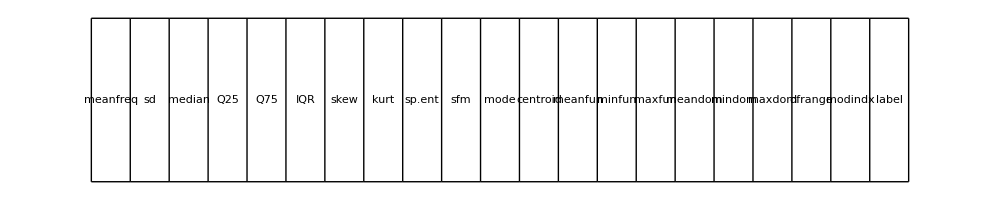
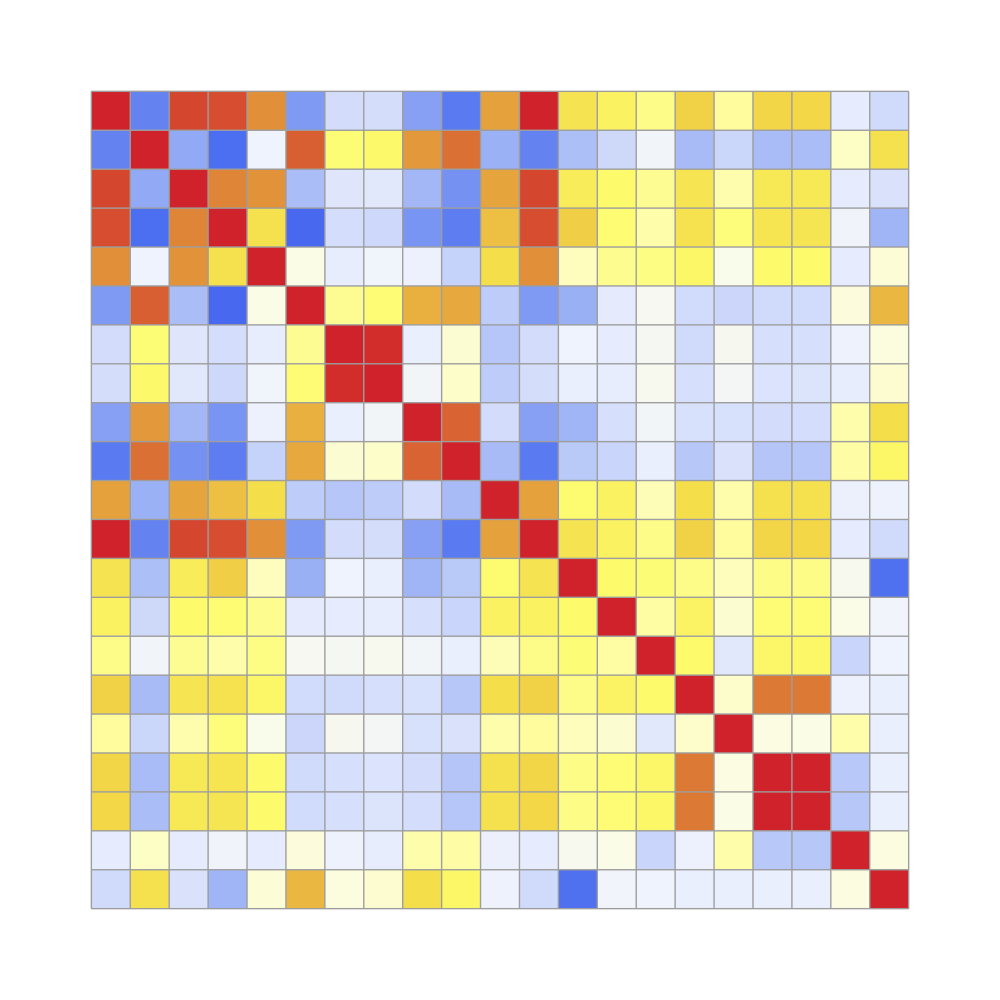
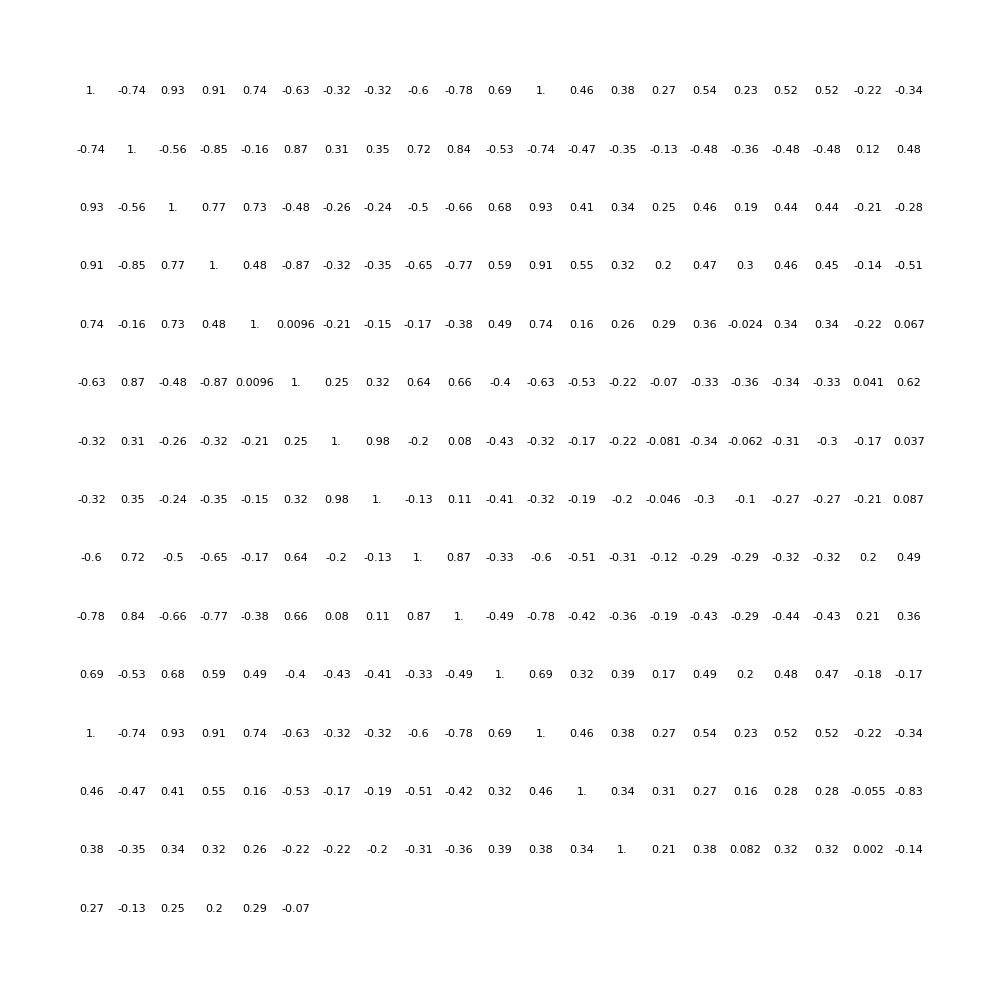
-Graphics-
-Graphics--Graphics--Graphics-

```mathematica
Column[{GraphicsRow[header,ImageSize->1000,Frame->All],Row[{GraphicsColumn[header,ImageSize->{50,1000},Frame->All],Overlay[{ArrayPlot[ccm,ColorFunction->(ColorData["TemperatureMap"][(1+#)/2]&),Frame->None,Mesh->True,PlotRangePadding->0,ImageSize->{1000,1000},ColorFunctionScaling->False],GraphicsGrid[Map[NumberForm[#,2]&,ccm,{2}],ImageSize->{1000,1000}]}]}]},Alignment->Right,Spacings->0]
```

SOME INFERENCES FROM THE ABOVE HEATMAP--
1) Mean frequency is moderately related to label.

2) IQR and label tend to have a strong positive co relation.

3) Spectral entropy is also quite highly corelated with the label while sfm is moderately related with label.

4) skewness and kurtosis aren’t much related with label.

5) meanfun is highly negatively corelated with the label.

6) Centroid and median have a high positive co relations expected from their formulae.

7) ALSO NOTE THAT MEANFREQ AND CENTROID ARE EXACTLY SAME FEATURES AS PER FORMULAE AND VALUES ALSO. HENCE THEIR CORELATION IS PERFCET 1. IN THAT CASE WE CAN DROP ANY COLUMN. note that centroid in general has a high degree of corelation with most of the other features.

SO I WILL DROP THE ‘CENTROID’ COLUMN.

8) sd is highly positively related to sfm and so is sp.ent to sd.

9) kurt and skew are also highly corelated.

10) meanfreq is highly related to medians well as Q25.

11) IQR is highly corelated to sd.

12) Finally self relation i.e of a feature to itself is equal to 1 as expected.

## Preparing the data:

I have dropped some columns which according to my analysis proved to be less useful or redundant,they are centroid,skew,kurt, mindom and maxdom.I have dropped the columns using excel and have reloaded the new data without those columns.

```mathematica
voiceData1=Import["Desktop/voice1.csv"];
header1=voiceData1[[1]];
datatest1=voiceData1[[2;;]];
voicedata2=Thread[header1->#]&/@datatest1//Map[Association]//Dataset;
```

```mathematica
voicedatas=voicedata2/.{"male"-> 1,"female"-> 0};
```

## Splitting the data into train and test sets:

I have splitted the data randomly into 80% of trainset and 20% of test set.

```mathematica
SeedRandom[123];
```

```mathematica
{dataTrain,dataTest}=TakeDrop[RandomSample[voicedatas],Round[Length[voicedatas]*0.8]];
```

```mathematica
Length[dataTrain]
```

2534

```mathematica
Length[dataTest]
```

634

```mathematica
dataTrain[1]//Dataset
```

Dataset[<>]

```mathematica
dataTest[1]
```

Dataset[<>]

## Classification algorithms:

I have used various methods:

1)Flattens     :-                                       		flattens out nested lists.

2)Classify        :-                                 		generates a ClassifierFunction[…] based on the examples and classes given.

3)ClassifierInformation     :-         		generates a report giving information on the classifier function classifier.
     ClassifierInformation[classifier,prop]

4)ConfusionMatrixPlot    :-          		generates a plot that gives a visual representation of the values of elements in a matrix.

5)ClassifierMeasurements   :-    		gives measurements associated with property prop when classifier is evaluated on test set.

```mathematica
trainsetFeatures=dataTrain[1;;Length[dataTrain],{"meanfreq", "sd","median", "Q25", "Q75",  "IQR", "sp.ent","sfm", "mode",  "meanfun","minfun","maxfun","meandom","dfrange","modindx","label"}];
```

```mathematica
trainsetFinal=Flatten[Normal@trainsetFeatures[1;;Length[dataTrain],{Most@#->Last@#}&],1];
```

```mathematica
testsetFeatures=dataTest[1;;Length[dataTest],{"meanfreq", "sd","median", "Q25", "Q75",  "IQR", "sp.ent","sfm", "mode",  "meanfun","minfun","maxfun","meandom","dfrange","modindx","label"}];
```

```mathematica
testsetFinal=Flatten[Normal@testsetFeatures[1;;Length[dataTest],{Most@#->Last@#}&],1];
```

## K-Nearest Neighbor

In pattern recognition, the k-nearest neighbors algorithm (k-NN) is a non-parametric method used for classification and regression. In both cases, the input consists of the k closest training examples in the feature space. ... If k = 1, then the object is simply assigned to the class of that single nearest neighbor.I have used parameter ”NeighborsNumber” to give the number of K.I have used [1,3,5,7,9] as K values.K must always be odd.

```mathematica
algoNN1=Classify[trainsetFinal,Method->{"NearestNeighbors","NeighborsNumber"-> 1}]
```

ClassifierFunction[…]

```mathematica
algoNN3=Classify[trainsetFinal,Method->{"NearestNeighbors","NeighborsNumber"-> 3}]
```

ClassifierFunction[…]

```mathematica
algoNN5=Classify[trainsetFinal,Method->{"NearestNeighbors","NeighborsNumber"-> 5}]
```

ClassifierFunction[…]

```mathematica
algoNN7=Classify[trainsetFinal,Method->{"NearestNeighbors","NeighborsNumber"-> 7}]
```

ClassifierFunction[…]

```mathematica
algoNN9=Classify[trainsetFinal,Method->{"NearestNeighbors","NeighborsNumber"-> 9}]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[algoNN1,"MethodDescription"]
```

The nearest neighbors classifier infers the class of a new example by analyzing its nearest neighbors in the feature space. In its simplest form, it picks the commonest class amongst the "k"-nearest neighbors.

The developed Classifier is applied to the test set

```mathematica
cmNN1=ClassifierMeasurements[algoNN1,testsetFinal];
```

```mathematica
cmNN3=ClassifierMeasurements[algoNN3,testsetFinal];
```

```mathematica
cmNN5=ClassifierMeasurements[algoNN5,testsetFinal];
```

```mathematica
cmNN7=ClassifierMeasurements[algoNN7,testsetFinal];
```

```mathematica
cmNN9=ClassifierMeasurements[algoNN9,testsetFinal];
```

Here the quality of the classification can be assessed with the following  Measurements: 

-Accuracy displays the fraction of correctly classified examples vs the Error, which is the fraction of incorrectly classified examples
-  F-Score identifies the F-score for each class - that means  a measure of a test’s accuracy. It considers both the precision p and the recall r of the test to compute the score: p is the number of correct positive results divided by the number of all positive results, and r is the number of correct positive results divided by the number of positive results that should have been returned. The F- score is the harmonic average of the precision and recall, where an F- score reaches its best value at 1 (perfect precision and recall) and worst at 0.
- Error displays the error rate - pendant to Accuracy.
- Precision - the fraction of relevant instances among the retrieved instances.

Several more classifier measurements are available.

```mathematica
cmNN1/@{"Accuracy","FScore","ConfusionFunction"}//TableForm
```

1.
<|0→1.,1→1.|>
<|0→<|0→305,1→0,Indeterminate→0|>,1→<|0→0,1→329,Indeterminate→0|>|>

```mathematica
cmNN3/@{"Accuracy","FScore","ConfusionFunction"}//TableForm
```

0.988959
<|0→0.988468,1→0.98941|>
<|0→<|0→300,1→5,Indeterminate→0|>,1→<|0→2,1→327,Indeterminate→0|>|>

```mathematica
cmNN5/@{"Accuracy","FScore","ConfusionFunction"}//TableForm
```

0.992114
<|0→0.991736,1→0.992459|>
<|0→<|0→300,1→5,Indeterminate→0|>,1→<|0→0,1→329,Indeterminate→0|>|>

```mathematica
cmNN7/@{"Accuracy","FScore","ConfusionFunction"}//TableForm
```

0.987382
<|0→0.986842,1→0.987879|>
<|0→<|0→300,1→5,Indeterminate→0|>,1→<|0→3,1→326,Indeterminate→0|>|>

```mathematica
cmNN9/@{"Accuracy","FScore","ConfusionFunction"}//TableForm
```

0.984227
<|0→0.983444,1→0.98494|>
<|0→<|0→297,1→8,Indeterminate→0|>,1→<|0→2,1→327,Indeterminate→0|>|>

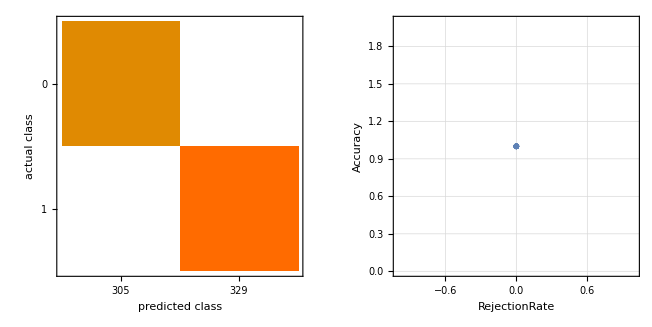

```mathematica
GraphicsRow[{cmNN1["ConfusionMatrixPlot"],cmNN1["AccuracyRejectionPlot"]}]
```

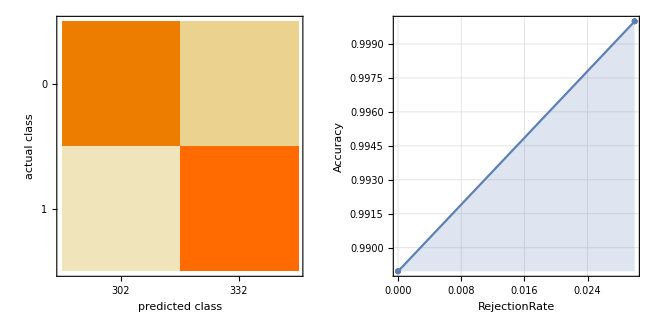

```mathematica
GraphicsRow[{cmNN3["ConfusionMatrixPlot"],cmNN3["AccuracyRejectionPlot"]}]
```

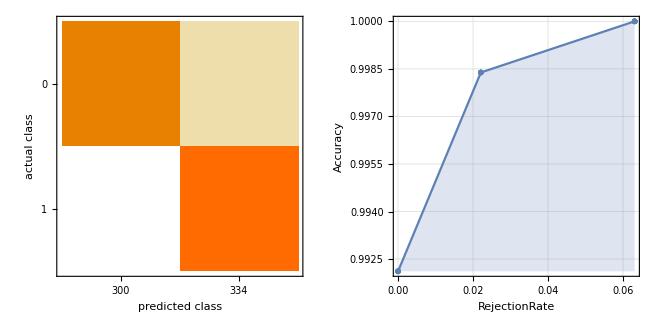

```mathematica
GraphicsRow[{cmNN5["ConfusionMatrixPlot"],cmNN5["AccuracyRejectionPlot"]}]
```

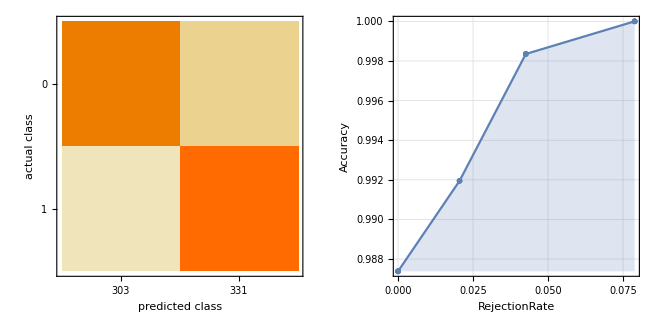

```mathematica
GraphicsRow[{cmNN7["ConfusionMatrixPlot"],cmNN7["AccuracyRejectionPlot"]}]
```

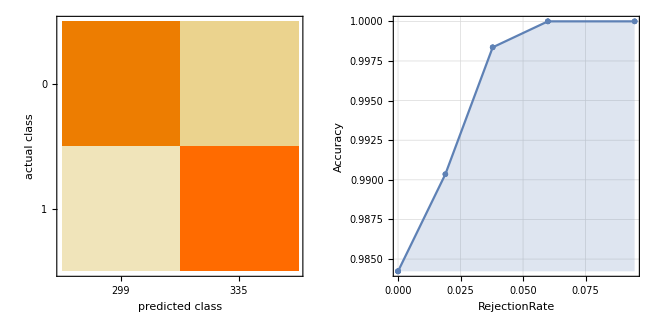

```mathematica
GraphicsRow[{cmNN9["ConfusionMatrixPlot"],cmNN9["AccuracyRejectionPlot"]}]
```

The Classifier Information gives me knowledge about the algorithm used in the classifier.

```mathematica
ClassifierInformation[algoNN1]
```

Classifier information
Input type | Mixed (number: 15)
Classes | ,,01
Method | NearestNeighbors
Accuracy | 97.8 % ± 0.47 %
Loss | 0.198 ± 0.0057
Single evaluation time | 1.99 ms/example
Batch evaluation speed | 68.4 examples/ms
Classifier memory | 481. kB
Training examples used | 2534 examples
Training time | 4.01 s
 |

```mathematica
ClassifierInformation[algoNN3]
```

Classifier information
Input type | Mixed (number: 15)
Classes | ,,01
Method | NearestNeighbors
Accuracy | 97.1 % ± 0.65 %
Loss | 0.115 ± 0.0087
Single evaluation time | 2.15 ms/example
Batch evaluation speed | 27.9 examples/ms
Classifier memory | 481. kB
Training examples used | 2534 examples
Training time | 2.36 s
 |

```mathematica
ClassifierInformation[algoNN5]
```

Classifier information
Input type | Mixed (number: 15)
Classes | ,,01
Method | NearestNeighbors
Accuracy | 97.7 % ± 0.61 %
Loss | 0.0863 ± 0.0082
Single evaluation time | 2.1 ms/example
Batch evaluation speed | 26.4 examples/ms
Classifier memory | 481. kB
Training examples used | 2534 examples
Training time | 2.22 s
 |

```mathematica
ClassifierInformation[algoNN7]
```

Classifier information
Input type | Mixed (number: 15)
Classes | ,,01
Method | NearestNeighbors
Accuracy | 97.3 % ± 0.53 %
Loss | 0.0824 ± 0.0072
Single evaluation time | 2.22 ms/example
Batch evaluation speed | 18.8 examples/ms
Classifier memory | 481. kB
Training examples used | 2534 examples
Training time | 2.23 s
 |

```mathematica
ClassifierInformation[algoNN9]
```

Classifier information
Input type | Mixed (number: 15)
Classes | ,,01
Method | NearestNeighbors
Accuracy | 97.2 % ± 0.56 %
Loss | 0.0765 ± 0.0071
Single evaluation time | 2.17 ms/example
Batch evaluation speed | 20.4 examples/ms
Classifier memory | 481. kB
Training examples used | 2534 examples
Training time | 2.2 s
 |

KNN classification gives the accuracy of 97.8% with K=1,with the loss very less equal to 0.198.

## logistic regression:

Logistic regression is a statistical method for analyzing a dataset in which there are one or more independent variables that determine an outcome. The outcome is measured with a dichotomous variable (in which there are only two possible outcomes).

```mathematica
LR=Classify[trainsetFinal,Method->"LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[algoLR,"MethodDescription"]
```

The logistic regression classifier models class probabilities with logistic functions of linear combinations of features. It is also called log-linear model, softmax regression, or maximum-entropy classifier.

```mathematica
confmatLR=ClassifierMeasurements[algoLR,testsetFinal];
confmatLR/@{"Accuracy","FScore","ConfusionFunction"}//TableForm
```

0.974763
<|0→0.97351,1→0.975904|>
<|0→<|0→294,1→11,Indeterminate→0|>,1→<|0→5,1→324,Indeterminate→0|>|>

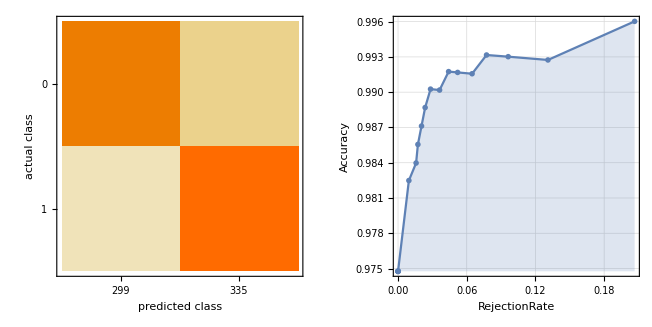

```mathematica
GraphicsRow[{confmatLR["ConfusionMatrixPlot"],confmatLR["AccuracyRejectionPlot"]}]
```

```mathematica
ClassifierInformation[LR]
```

Classifier information
Input type | Mixed (number: 15)
Classes | ,,01
Method | LogisticRegression
Accuracy | 98.5 % ± 0.85 %
Loss | 0.0404 ± 0.012
Single evaluation time | 1.94 ms/example
Batch evaluation speed | 198. examples/ms
Classifier memory | 282. kB
Training examples used | 2534 examples
Training time | 3.93 s
 |

Logistic Regression gives accuracy of 98.5% with very less loss of 0.04.

## RANDOM FOREST

Random forests  are an ensemble learning method for classification, regression and other tasks, that operate by constructing a multitude of decision trees at training time and outputting the class that is the mode of the classes (classification) or mean prediction (regression) of the individual trees. Here we will carry out a classification. 
First I define the algorithm by specifying the dataset and the Method.

```mathematica
RF=Classify[trainsetFinal,Method->"RandomForest"]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[RF,"MethodDescription"]
```

The random forest classifier uses an ensemble of decision trees to predict the class. Each decision tree has been trained on a random subset of the training set, and only uses a random subset of the features.

```mathematica
confmatRF=ClassifierMeasurements[RF,testsetFinal];
```

```mathematica
confmatRF/@{"Accuracy","FScore","Error",  "Precision"}//TableForm
```

0.988959
<|0→0.988506,1→0.989378|>
0.011041
<|0→0.990132,1→0.987879|>

The confusion matrix blot below counts c[ij] of class i examples classified as class j.

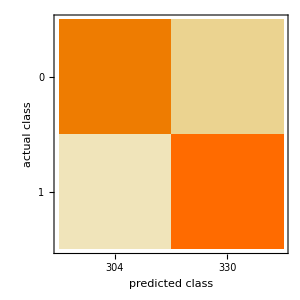

```mathematica
confmatRF["ConfusionMatrixPlot"]
```

This plot shows the accuracy as function of the rejection rate

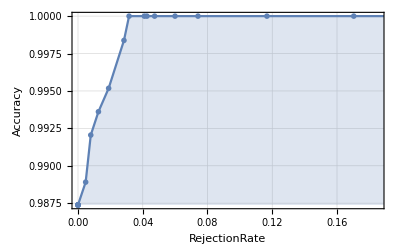

```mathematica
confmatRF["AccuracyRejectionPlot"]
```

```mathematica
ClassifierInformation[RF]
```

Classifier information
Input type | Mixed (number: 15)
Classes | ,,01
Method | RandomForest
Accuracy | 97.7 % ± 0.48 %
Loss | 0.0787 ± 0.0081
Single evaluation time | 5.49 ms/example
Batch evaluation speed | 21.3 examples/ms
Classifier memory | 281. kB
Training examples used | 2534 examples
Training time | 5.49 s
 |

Random Forest comes with the accuracy of 97.7% with very less loss of 0.078.

## Artificial Neural Network

Artificial neural networks (ANNs) or connectionist systems are computing systems inspired by the biological neural networks that constitute animal brains. Such systems learn (progressively improve performance) to do tasks by considering examples, generally without task-specific programming.

```mathematica
ANN=Classify[trainsetFinal,Method->"NeuralNetwork"]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[ANN,"MethodDescription"]
```

An neural networks is composed of layers of artificial neuron units. Each 
unit computes its value as a function of the unit values in the previous layer. Information 
is processed layer by layer from the feature layer to the output layer which gives the class probabilities. It is 
also called a feed-forward neural network or a multi-layer perceptron.

```mathematica
confmatANN=ClassifierMeasurements[ANN,testsetFinal];
confmatANN/@{"Accuracy","FScore","ConfusionFunction"}//TableForm
```

0.701893
<|0→0.573363,1→0.770909|>
<|0→<|0→127,1→178,Indeterminate→0|>,1→<|0→11,1→318,Indeterminate→0|>|>

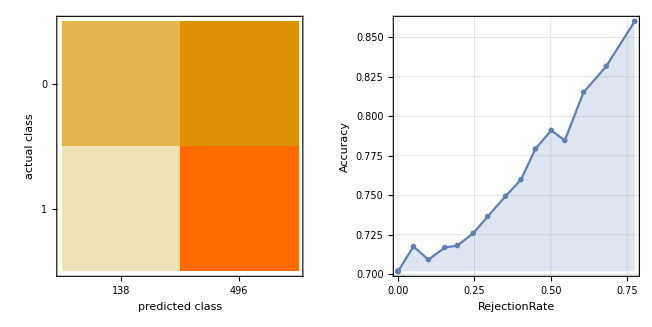

```mathematica
GraphicsRow[{confmatANN["ConfusionMatrixPlot"], confmatANN["AccuracyRejectionPlot"]}]
```

```mathematica
ClassifierInformation[ANN]
```

Classifier information
Input type | Mixed (number: 15)
Classes | ,,01
Method | NeuralNetwork
Accuracy | 92.2 % ± 1.2 %
Loss | 0.188 ± 0.02
Single evaluation time | 3.14 ms/example
Batch evaluation speed | 77.5 examples/ms
Classifier memory | 1.56 MB
Training examples used | 2534 examples
Training time | 47. s
 |

Artificial Neural Network has accuracy of 92.2% with the loss equal to 0.188.

## Support Vector Machine

Support Vector Machines are based on the concept of decision planes that define decision boundaries. A decision plane is one that separates between a set of objects having different class memberships.

```mathematica
SV=Classify[trainsetFinal,Method->"SupportVectorMachine"]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[SV,"MethodDescription"]
```

The support vector machine classifier separates the training data into two classes using a 
			maximum-margin hyperplane. The original feature space can be mapped into a higher dimensional space to 
			improve linear separability. The multi-class classification problem is reduced to a set of binary 
			classification problems.

```mathematica
confmatSV=ClassifierMeasurements[SV,testsetFinal];
confmatSV/@{"Accuracy","FScore","ConfusionFunction"}//TableForm
```

0.98265
<|0→0.981938,1→0.983308|>
<|0→<|0→299,1→6,Indeterminate→0|>,1→<|0→5,1→324,Indeterminate→0|>|>

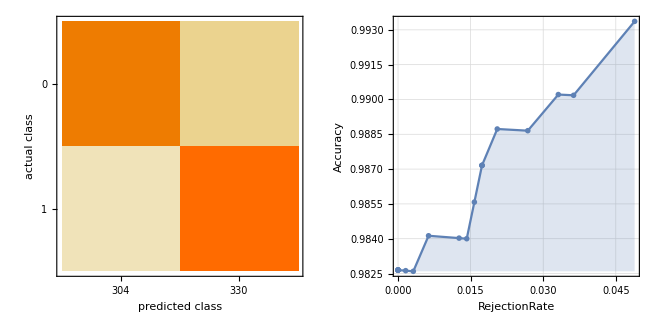

```mathematica
GraphicsRow[{confmatSV["ConfusionMatrixPlot"], confmatSV["AccuracyRejectionPlot"]}]
```

```mathematica
ClassifierInformation[SV]
```

Classifier information
Input type | Mixed (number: 15)
Classes | ,,01
Method | SupportVectorMachine
Accuracy | 98.6 % ± 1.2 %
Loss | 0.0108 ± 0.0081
Single evaluation time | 3.26 ms/example
Batch evaluation speed | 36.1 examples/ms
Classifier memory | 411. kB
Training examples used | 2534 examples
Training time | 7.18 s
 |

Support Random Vector gives accuracy equal to 98.6% with very less loss of 0.01.

## Accuracy Table:

```mathematica
acctable={{"CLASSIFICATION METHOD","ACCURACY(%)"},{"NearestNeighbor(k=1)",97.8},{"NearestNeighbor(k=3)",97.1},{"NearestNeighbor(k=5)",97.7},{"NearestNeighbor(k=7)",97.3},{"NearestNeighbor(k=9)",97.2},{"Logistic Regression",98.5},{"Random Forest",97.7},{"Artificial Neural Network",92.2},{"Support Vector Machine",98.6}}//Dataset
```

Dataset[<>]

NOTE: The accuracy percentage may vary slightly if we run the classification methods again.

## Conclusion:

Support Vector Machine gives an amazing accuracy of around 98.6%,followed by Logistic regression which is not too far and is about 98.5%.Nearest Neighbor classification method takes third place with accuracy equal to 97.8 with k=1,then comes Random Forest with accuracy equal to 97.7,Artificial Neural Network gives less accuracy comparatively of about 92.2%.
The Accuracy can be increased  by tuning the algorithm parameters.